# Non-Minimally Coupled Loop Quantum Cosmology

## Geometry of Spacetime

Clearing the values of symbols:

```mathematica
Clear[coord,metric,inversemetric,affine,t,x,y,z]
```

Setting the dimension:

```mathematica
nc:=4
```

Defining a list of coordinates:

```mathematica
coord:={t,x,y,z}
```

Defining the metric:

```mathematica
metric:=({{-1, 0, 0, 0}, {0, (a(t))^2, 0, 0}, {0, 0, (a(t))^2, 0}, {0, 0, 0, (a(t))^2}})
```

```mathematica
MatrixForm[metric]
```

(-1 | 0 | 0 | 0
0 | a[t]^2 | 0 | 0
0 | 0 | a[t]^2 | 0
0 | 0 | 0 | a[t]^2)

```mathematica
√(-Det[metric])
```

√(a[t]^6)

Calculating the inverse metric:

```mathematica
inversemetric:=Simplify[metric]
```

```mathematica
MatrixForm[inversemetric]
```

(-1 | 0 | 0 | 0
0 | 1/a[t]^2 | 0 | 0
0 | 0 | 1/a[t]^2 | 0
0 | 0 | 0 | 1/a[t]^2)

Calculating the Christoffel symbols of the second kind:

```mathematica
affine:=affine=Simplify[Table[1/2 ∑_(ρ=1)^nc inversemetric⟦μ,ρ⟧ (-(∂metric⟦ν,λ⟧)/(∂coord⟦ρ⟧)+(∂metric⟦ρ,λ⟧)/(∂coord⟦ν⟧)+(∂metric⟦ρ,ν⟧)/(∂coord⟦λ⟧)),{ν,1,nc},{λ,1,nc},{μ,1,nc}]]
```

Displaying the Christoffel symbols of the second kind:

```mathematica
listaffine:=Table[If[affine⟦ν,λ,μ⟧=!=0,{Style[Subscript[Γ, Row[{coord⟦ν⟧,coord⟦λ⟧}]]^coord⟦μ⟧,18],"=",Style[affine⟦ν,λ,μ⟧,14]}],{λ,1,nc},{ν,1,λ},{μ,1,nc}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],3],TableSpacing->{1,2}]
```

Γ_tx^x | = | a'[t]/a[t]
Γ_xx^t | = | a[t] a'[t]
Γ_ty^y | = | a'[t]/a[t]
Γ_yy^t | = | a[t] a'[t]
Γ_tz^z | = | a'[t]/a[t]
Γ_zz^t | = | a[t] a'[t]

Defining the Riemann tensor:

```mathematica
riemann:=riemann=Table[∑_(λ=1)^nc (affine⟦ρ,λ,μ⟧ affine⟦ν,σ,λ⟧-affine⟦σ,λ,μ⟧ affine⟦ν,ρ,λ⟧)-(∂affine⟦ν,ρ,μ⟧)/(∂coord⟦σ⟧)+(∂affine⟦ν,σ,μ⟧)/(∂coord⟦ρ⟧),{μ,1,nc},{ν,1,nc},{ρ,1,nc},{σ,1,nc}]
```

Defining the Riemann tensor with lower indices:

```mathematica
riemannDn:=riemannDn=Table[Simplify[∑_(κ=1)^nc metric⟦μ,κ⟧ riemann⟦κ,ν,ρ,σ⟧],{μ,1,nc},{ν,1,nc},{ρ,1,nc},{σ,1,nc}]
```

```mathematica
listRiemann:=Table[If[riemannDn⟦μ,ν,ρ,σ⟧=!=0,{Style[Subscript[R, Row[{coord⟦μ⟧,coord⟦ν⟧,coord⟦ρ⟧,coord⟦σ⟧}]],16],"=",riemannDn⟦μ,ν,ρ,σ⟧}],{ν,1,nc},{μ,1,ν},{σ,1,nc},{ρ,1,σ}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listRiemann],Null],3],TableSpacing->{2,2}]
```

R_txtx | = | -a[t] a''[t]
R_tyty | = | -a[t] a''[t]
R_xyxy | = | a[t]^2 a'[t]^2
R_tztz | = | -a[t] a''[t]
R_xzxz | = | a[t]^2 a'[t]^2
R_yzyz | = | a[t]^2 a'[t]^2

Defining the Ricci tensor:

```mathematica
ricci:=ricci=Table[Simplify[∑_(ρ=1)^nc riemann⟦ρ,μ,ρ,ν⟧],{μ,1,nc},{ν,1,nc}]
```

```mathematica
listRicci:=Table[If[ricci⟦μ,ν⟧=!=0,{Style[Subscript[R, Row[{coord⟦μ⟧,coord⟦ν⟧}]],16],"=",Style[ricci⟦μ,ν⟧,16]}],{ν,1,nc},{μ,1,ν}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listRicci],Null],3],TableSpacing->{1,2}]
```

R_tt | = | -(3 a''[t])/a[t]
R_xx | = | 2 a'[t]^2+a[t] a''[t]
R_yy | = | 2 a'[t]^2+a[t] a''[t]
R_zz | = | 2 a'[t]^2+a[t] a''[t]

Defining the Ricci scalar:

```mathematica
ricciscalar:=ricciscalar=Simplify[∑_(ν=1)^nc (∑_(μ=1)^nc inversemetric⟦μ,ν⟧ ricci⟦ν,μ⟧)]
```

```mathematica
ricciscalar
```

(6 (a'[t]^2+a[t] a''[t]))/a[t]^2

## Classical Equation of Motion

Define the Lagrangian

```mathematica
ℒ:=Expand[√(-Det[metric]) (-∑_(ν=1)^nc (∑_(μ=1)^nc 1/2 inversemetric⟦μ,ν⟧ (∂ϕ(t))/(∂coord⟦μ⟧) (∂ϕ(t))/(∂coord⟦ν⟧))+(ricciscalar u(ϕ(t)))/(2 κ)-v(ϕ(t)))]
```

```mathematica
Expand[ℒ]
```

-√(a[t]^6) v[ϕ[t]]+(3 √(a[t]^6) u[ϕ[t]] a'[t]^2)/(κ a[t]^2)+1/2 √(a[t]^6) ϕ'[t]^2+(3 √(a[t]^6) u[ϕ[t]] a''[t])/(κ a[t])

```mathematica
ℒ=Expand[ℒ/.a''(t) u(ϕ(t))->-((2 (a'(t))^2 u(ϕ(t)))/(a(t))+a'(t) (∂u(ϕ(t)))/(∂t))/.√((a(t))^6)->(a(t))^3]
```

-a[t]^3 v[ϕ[t]]-(3 a[t] u[ϕ[t]] a'[t]^2)/κ-(3 a[t]^2 a'[t] u'[ϕ[t]] ϕ'[t])/κ+1/2 a[t]^3 ϕ'[t]^2

```mathematica
Expand[(ℒ/.a'(t)->a(t) H(t))/(a(t))^3]
```

-(3 H[t]^2 u[ϕ[t]])/κ-v[ϕ[t]]-(3 H[t] u'[ϕ[t]] ϕ'[t])/κ+1/2 ϕ'[t]^2

Equation of motions

```mathematica
eoma=Expand[∂/(∂t)(∂ℒ)/(∂a'(t))-(∂ℒ)/(∂a(t))]
```

3 a[t]^2 v[ϕ[t]]-(3 u[ϕ[t]] a'[t]^2)/κ-(6 a[t] a'[t] u'[ϕ[t]] ϕ'[t])/κ-3/2 a[t]^2 ϕ'[t]^2-(6 a[t] u[ϕ[t]] a''[t])/κ-(3 a[t]^2 ϕ'[t]^2 u''[ϕ[t]])/κ-(3 a[t]^2 u'[ϕ[t]] ϕ''[t])/κ

```mathematica
Expand[-(eoma/.a'(t)->a(t) H(t))/(3 (a(t))^2)]
```

(H[t]^2 u[ϕ[t]])/κ-v[ϕ[t]]+(2 H[t] u'[ϕ[t]] ϕ'[t])/κ+1/2 ϕ'[t]^2+(2 u[ϕ[t]] a''[t])/(κ a[t])+(ϕ'[t]^2 u''[ϕ[t]])/κ+(u'[ϕ[t]] ϕ''[t])/κ

```mathematica
eomp=Expand[∂/(∂t)(∂ℒ)/(∂ϕ'(t))-(∂ℒ)/(∂ϕ(t))]
```

-(3 a[t] a'[t]^2 u'[ϕ[t]])/κ+a[t]^3 v'[ϕ[t]]+3 a[t]^2 a'[t] ϕ'[t]-(3 a[t]^2 u'[ϕ[t]] a''[t])/κ+a[t]^3 ϕ''[t]

```mathematica
Expand[(eomp/.a'(t)->a(t) H(t))/(a(t))^3]
```

-(3 H[t]^2 u'[ϕ[t]])/κ+v'[ϕ[t]]+3 H[t] ϕ'[t]-(3 u'[ϕ[t]] a''[t])/(κ a[t])+ϕ''[t]

```mathematica
Subscript[π, ϕ]=(∂ℒ)/(∂ϕ'(t))
```

-(3 a[t]^2 a'[t] u'[ϕ[t]])/κ+a[t]^3 ϕ'[t]

```mathematica
Subscript[π, a]=(∂ℒ)/(∂a'(t))
```

-(6 a[t] u[ϕ[t]] a'[t])/κ-(3 a[t]^2 u'[ϕ[t]] ϕ'[t])/κ

```mathematica
ℋ=Expand[Subscript[π, a] a'(t)+Subscript[π, ϕ] ϕ'(t)-ℒ]
```

a[t]^3 v[ϕ[t]]-(3 a[t] u[ϕ[t]] a'[t]^2)/κ-(3 a[t]^2 a'[t] u'[ϕ[t]] ϕ'[t])/κ+1/2 a[t]^3 ϕ'[t]^2

```mathematica
Expand[(ℋ/.a'(t)->a(t) H(t))/(a(t))^3]
```

-(3 H[t]^2 u[ϕ[t]])/κ+v[ϕ[t]]-(3 H[t] u'[ϕ[t]] ϕ'[t])/κ+1/2 ϕ'[t]^2

Slow-Roll Approximation

```mathematica
eomaSR:=Expand[eoma/.{a''(t)->a(t) (H(t))^2 (1-ζ ϵ),ϕ''(t)->ζ Subscript[δ, ϕ] H(t) ϕ'(t),(ϕ'(t))^2->(2 ζ (H(t))^2 Subscript[δ, X] u(ϕ(t)))/κ,ϕ'(t) u'(ϕ(t))->ζ H(t) Subscript[δ, U] u(ϕ(t)),H(t)->(a'(t))/(a(t))}]
```

```mathematica
eomaSR0=Expand[Coefficient[eomaSR,ζ,0]]
```

-(6 a[t]^2 H[t]^2 u[ϕ[t]])/κ+3 a[t]^2 v[ϕ[t]]-(3 u[ϕ[t]] a'[t]^2)/κ

```mathematica
Expand[-(eomaSR0/.a'(t)->a(t) H(t))/(3 (a(t))^2)]
```

(3 H[t]^2 u[ϕ[t]])/κ-v[ϕ[t]]

```mathematica
eompSR:=Expand[eomp/.{a''(t)->a(t) (H(t))^2 (1-ζ ϵ),ϕ''(t)->ζ Subscript[δ, ϕ] H(t) ϕ'(t),(ϕ'(t))^2->2 ζ (H(t))^2 Subscript[δ, X] u(ϕ(t)),ϕ'(t) U'(ϕ(t))->ζ H(t) Subscript[δ, U] u(ϕ(t)),H(t)->(a'(t))/(a(t))}]
```

```mathematica
eompSR0=Expand[Coefficient[eompSR,ζ,0]]
```

-(3 a[t]^3 H[t]^2 u'[ϕ[t]])/κ-(3 a[t] a'[t]^2 u'[ϕ[t]])/κ+a[t]^3 v'[ϕ[t]]+3 a[t]^2 a'[t] ϕ'[t]

```mathematica
Expand[-(eompSR0/.a'(t)->a(t) H(t))/(a(t))^3]
```

(6 H[t]^2 u'[ϕ[t]])/κ-v'[ϕ[t]]-3 H[t] ϕ'[t]

Solve for H and ϕ’(t)

```mathematica
HSol(t):=Expand[Values[Solve[Expand[-(eomaSR0/.a'(t)->a(t) H(t))/(3 (a(t))^2)]==0,H(t)]]⟦2⟧⟦1⟧]
```

```mathematica
HSol(t)
```

(√κ √v[ϕ[t]])/(√3 √u[ϕ[t]])

```mathematica
HC2=FullSimplify[(HSol(t))^2]
```

(κ v[ϕ[t]])/(3 u[ϕ[t]])

```mathematica
ϕtSol(t_):=Expand[Values[Solve[Expand[-(eompSR0/.a'(t)->a(t) H(t))/(a(t))^3]==0,ϕ'(t)]]⟦1⟧⟦1⟧]
```

```mathematica
ϕtSol(t)
```

(2 H[t] u'[ϕ[t]])/κ-v'[ϕ[t]]/(3 H[t])

```mathematica
ϕtHC=FullSimplify[(ϕtSol(t))/(H(t))]
```

(2 u'[ϕ[t]])/κ-v'[ϕ[t]]/(3 H[t]^2)

```mathematica
ϕtH=Expand[ϕtHC/.H(t)->HSol(t)]
```

(2 u'[ϕ[t]])/κ-(u[ϕ[t]] v'[ϕ[t]])/(κ v[ϕ[t]])

Equation of motions

## Loop Quantum Cosmology

```mathematica
ℒ
```

-a[t]^3 v[ϕ[t]]-(3 a[t] u[ϕ[t]] a'[t]^2)/κ-(3 a[t]^2 a'[t] u'[ϕ[t]] ϕ'[t])/κ+1/2 a[t]^3 ϕ'[t]^2

```mathematica
ℋ
```

a[t]^3 v[ϕ[t]]-(3 a[t] u[ϕ[t]] a'[t]^2)/κ-(3 a[t]^2 a'[t] u'[ϕ[t]] ϕ'[t])/κ+1/2 a[t]^3 ϕ'[t]^2

```mathematica
ℐ=Expand[ℒ/.ϕ'(t)->π/(a(t))^3]/.(a(t))^3->(a(t))^3 (Subscript[D, l](t))^m/.1/(a(t))^3->(Subscript[D, l](t))^(-(n+1))/(a(t))^3/.π->(a(t))^3 ϕ'(t)
```

-a[t]^3 v[ϕ[t]] D_l[t]^m-(3 a[t] u[ϕ[t]] a'[t]^2)/κ-(3 a[t]^2 a'[t] u'[ϕ[t]] ϕ'[t])/κ+1/2 a[t]^3 D_l[t]^(-1-n) ϕ'[t]^2

```mathematica
FullSimplify[(ℐ/.a'(t)->H a(t))/(a(t))^3]
```

-v[ϕ[t]] D_l[t]^m+1/2 D_l[t]^(-1-n) ϕ'[t]^2-(3 H (H u[ϕ[t]]+u'[ϕ[t]] ϕ'[t]))/κ

```mathematica
eomalqg=FullSimplify[∂/(∂t)(∂ℐ)/(∂a'(t))-(∂ℐ)/(∂a(t))]
```

(3 (-2 u[ϕ[t]] a'[t]^2-4 a[t] (a'[t] u'[ϕ[t]] ϕ'[t]+u[ϕ[t]] a''[t])+a[t]^2 (2 κ v[ϕ[t]] D_l[t]^m+ϕ'[t]^2 (-κ D_l[t]^(-1-n)-2 u''[ϕ[t]])-2 u'[ϕ[t]] ϕ''[t])))/(2 κ)

```mathematica
Expand[-eomalqg/(3 (a(t))^2)/.a'(t)->a(t) H(t)]
```

(H[t]^2 u[ϕ[t]])/κ-v[ϕ[t]] D_l[t]^m+(2 H[t] u'[ϕ[t]] ϕ'[t])/κ+1/2 D_l[t]^(-1-n) ϕ'[t]^2+(2 u[ϕ[t]] a''[t])/(κ a[t])+(ϕ'[t]^2 u''[ϕ[t]])/κ+(u'[ϕ[t]] ϕ''[t])/κ

```mathematica
eomplqg=FullSimplify[∂/(∂t)(∂ℐ)/(∂ϕ'(t))-(∂ℐ)/(∂ϕ(t))]
```

a[t] (a[t]^2 D_l[t]^m v'[ϕ[t]]-(3 u'[ϕ[t]] (a'[t]^2+a[t] a''[t]))/κ+a[t] D_l[t]^(-2-n) (-((1+n) a[t] ϕ'[t] D_l'[t])+D_l[t] (3 a'[t] ϕ'[t]+a[t] ϕ''[t])))

```mathematica
Expand[eomplqg/(a(t))^3/.a'(t)->a(t) H(t)]
```

-(3 H[t]^2 u'[ϕ[t]])/κ+D_l[t]^m v'[ϕ[t]]+3 H[t] D_l[t]^(-1-n) ϕ'[t]-D_l[t]^(-2-n) ϕ'[t] D_l'[t]-n D_l[t]^(-2-n) ϕ'[t] D_l'[t]-(3 u'[ϕ[t]] a''[t])/(κ a[t])+D_l[t]^(-1-n) ϕ''[t]

```mathematica
-(3 a''(t) u'(ϕ(t)))/(κ a(t))+3 H(t) ϕ'(t) (Subscript[D, l](t))^(-n-1)+(Subscript[D, l](t))^m v'(ϕ(t))+ϕ''(t) (Subscript[D, l](t))^(-n-1)-n ϕ'(t) (Subscript[D, l](t))^(-n-2) Subscript[D, l]'(t)-ϕ'(t) (Subscript[D, l](t))^(-n-2) Subscript[D, l]'(t)-(3 (H(t))^2 u'(ϕ(t)))/κ/.{Subscript[D, l](t)->Subscript[D, l],u'(ϕ(t))->u',H(t)->H,a(t)->a,a''(t)->ä,ϕ''(t)->ϕ̈,ϕ'(t)->ϕ̇,Subscript[D, l]'(t)->OverDot[Subscript[D, l]],v'(ϕ(t))->v'}
```

-ϕ̇ OverDot[D_l] D_l^(-2-n)-n ϕ̇ OverDot[D_l] D_l^(-2-n)+3 H ϕ̇ D_l^(-1-n)+ϕ̈ D_l^(-1-n)-(3 H^2 u')/κ-(3 ä u')/(a κ)+D_l^m v'

```mathematica
𝒬=Expand[ℋ/.ϕ'(t)->π/(a(t))^3]/.(a(t))^3->(a(t))^3 (Subscript[D, l](t))^m/.1/(a(t))^3->(Subscript[D, l](t))^(-(n+1))/(a(t))^3/.π->(a(t))^3 ϕ'(t)
```

a[t]^3 v[ϕ[t]] D_l[t]^m-(3 a[t] u[ϕ[t]] a'[t]^2)/κ-(3 a[t]^2 a'[t] u'[ϕ[t]] ϕ'[t])/κ+1/2 a[t]^3 D_l[t]^(-1-n) ϕ'[t]^2

```mathematica
FullSimplify[(𝒬/.a'(t)->H a(t))/(a(t))^3]
```

v[ϕ[t]] D_l[t]^m+1/2 D_l[t]^(-1-n) ϕ'[t]^2-(3 H (H u[ϕ[t]]+u'[ϕ[t]] ϕ'[t]))/κ

Slow Roll Approximation

```mathematica
eomalqgSR:=FullSimplify[Expand[eomalqg]/.{a''(t)->a(t) (H(t))^2 (1-ζ ϵ),ϕ''(t)->ζ Subscript[δ, ϕ] H(t) ϕ'(t),(ϕ'(t))^2->2 ζ (H(t))^2 Subscript[δ, X] u(ϕ(t)),ϕ'(t) u'(ϕ(t))->ζ H(t) Subscript[δ, u] u(ϕ(t)),Subscript[D, l]'(t)->ζ Subscript[δ, D] H(t) Subscript[D, l](t),H(t)->(a'(t))/(a(t))}]
```

```mathematica
eomalqgSR0=FullSimplify[Coefficient[eomalqgSR,ζ,0]]
```

3 a[t]^2 v[ϕ[t]] D_l[t]^m-(3 u[ϕ[t]] (2 a[t]^2 H[t]^2+a'[t]^2))/κ

```mathematica
FullSimplify[-(eomalqgSR0/.a'(t)->a(t) H(t))/(3 (a(t))^2)]
```

(3 H[t]^2 u[ϕ[t]])/κ-v[ϕ[t]] D_l[t]^m

```mathematica
eomplqgSR:=FullSimplify[Expand[eomplqg]/.{a''(t)->a(t) (H(t))^2 (1-ζ ϵ),ϕ''(t)->ζ Subscript[δ, ϕ] H(t) ϕ'(t),(ϕ'(t))^2->2 ζ (H(t))^2 Subscript[δ, X] u(ϕ(t)),ϕ'(t) u'(ϕ(t))->ζ H(t) Subscript[δ, u] u(ϕ(t)),F''(ϕ(t))->ζ K,Subscript[D, l]'(t)->ζ Subscript[δ, D] H(t) Subscript[D, l](t),H(t)->(a'(t))/(a(t))}]
```

```mathematica
eomplqgSR0=FullSimplify[Coefficient[eomplqgSR,ζ,0]]
```

(a[t] (-3 a'[t]^2 u'[ϕ[t]]+a[t]^2 (-3 H[t]^2 u'[ϕ[t]]+κ D_l[t]^m v'[ϕ[t]])+3 κ a[t] D_l[t]^(-1-n) a'[t] ϕ'[t]))/κ

```mathematica
FullSimplify[(eomplqgSR0/.a'(t)->a(t) H(t))/(a(t))^3]
```

-(6 H[t]^2 u'[ϕ[t]])/κ+D_l[t]^m v'[ϕ[t]]+3 H[t] D_l[t]^(-1-n) ϕ'[t]

```mathematica
HlqgSol(t):=FullSimplify[Values[Solve[Expand[eomalqgSR0/.a'(t)->a(t) H(t)]==0,H(t)]]⟦2⟧⟦1⟧]
```

```mathematica
HlqgSol(t)
```

(√κ √v[ϕ[t]] D_l[t]^(m/2))/(√3 √u[ϕ[t]])

```mathematica
(HlqgSol(t))^2/.{u(ϕ(t))->u,u'(ϕ(t))->u',Subscript[D, l](t)->Subscript[D, l],v(ϕ(t))->v}
```

(v κ D_l^m)/(3 u)

```mathematica
ϕtlqgSol(t):=Expand[Values[Solve[Expand[eomplqgSR0/.a'(t)->a(t) H(t)]==0,ϕ'(t)]]⟦1⟧⟦1⟧]
```

```mathematica
ϕtlqgSol(t)
```

(2 H[t] D_l[t]^(1+n) u'[ϕ[t]])/κ-(D_l[t]^(1+m+n) v'[ϕ[t]])/(3 H[t])

```mathematica
ϕtHlqg=Expand[FullSimplify[(ϕtlqgSol(t))/(H(t))]/.H(t)->HlqgSol(t)]
```

(2 D_l[t]^(1+n) u'[ϕ[t]])/κ-(u[ϕ[t]] D_l[t]^(1+n) v'[ϕ[t]])/(κ v[ϕ[t]])

```mathematica
ϕtHex=FullSimplify[FullSimplify[(ϕtlqgSol(t))/(H(t))]/.{H(t)->H,u(ϕ(t))->F,u'(ϕ(t))->u',u''(ϕ(t))->u'',Subscript[D, l](t)->Subscript[D, l],v(ϕ(t))->v,v'(ϕ(t))->v'}]
```

1/3 D_l^(1+n) ((6 u')/κ-(D_l^m v')/H^2)

## Probability of Inflation

```mathematica
Subscript[P, ϕ]=FullSimplify[(∂ℐ)/(∂ϕ'(t))/.{a'(t)->a(t) H(t)}]/.a(t)->SubStar[a] √q
```

q^(3/2) a_*^3 (-(3 H[t] u'[ϕ[t]])/κ+D_l[t]^(-1-n) ϕ'[t])

```mathematica
Subscript[B, q]=FullSimplify[(∂(Subscript[P, ϕ]/.ϕ'(t)->ϕtlqgSol(t)))/(∂H(t))]
```

(q^(3/2) a_*^3 (-3 H[t]^2 u'[ϕ[t]]+κ D_l[t]^m v'[ϕ[t]]))/(3 κ H[t]^2)

```mathematica
Expand[FullSimplify[Subscript[B, q]/.{Subscript[D, l](t)->Subscript[D, l],u'(ϕ(t))->u',H(t)->H,u''(ϕ(t))->u'',v'(ϕ(t))->v'}]]
```

-(q^(3/2) a_*^3 u')/κ+(q^(3/2) D_l^m a_*^3 v')/(3 H^2)

## Potential with Rϕ^2 Coupling

```mathematica
u(ϕ_):=ξ ϕ^2+1;v(ϕ_):=λ ϕ^(1/3)
```

```mathematica
FullSimplify[HlqgSol(t)^2]
```

(κ λ ϕ[t]^(1/3) D_l[t]^m)/(3+3 ξ ϕ[t]^2)

```mathematica
Expand[ϕtHlqg]
```

-D_l[t]^(1+n)/(3 κ ϕ[t])+(11 ξ ϕ[t] D_l[t]^(1+n))/(3 κ)

```mathematica
Simplify[ϕtHlqg]
```

((-1+11 ξ ϕ[t]^2) D_l[t]^(1+n))/(3 κ ϕ[t])

```mathematica
ReplaceAll[Subscript[P, ϕ],{H[t]->H, ϕ[t]->ϕ,Subscript[D, l][t]->Subscript[D, l],ϕ'[t]->OverDot[ϕ,1]}]
```

q^(3/2) (-(6 H ξ ϕ)/κ+ϕ̇ D_l^(-1-n)) a_*^3

```mathematica
ReplaceAll[Subscript[B, q],{H[t]->H, ϕ[t]->ϕ,Subscript[D, l][t]->Subscript[D, l],ϕ'[t]->OverDot[ϕ,1]}]
```

(q^(3/2) (-6 H^2 ξ ϕ+(κ λ D_l^m)/(3 ϕ^(2/3))) a_*^3)/(3 H^2 κ)

```mathematica
probint=∫(∫Subscript[B, q] ⅆH(t)/.H(t)->√((HlqgSol(t))^2)/.ϕ(t)->ϕ)ⅆϕ
```

-(2 q^(3/2) (3+3 ξ ϕ^2) a_*^3 √((κ λ ϕ^(1/3) D_l[t]^m)/(3+3 ξ ϕ^2)))/(3 κ)

```mathematica
prob=FullSimplify[(probint/.ϕ->Subscript[ϕ, f]/.Subscript[D, l][t]->Subscript[D, f])-(probint/.ϕ->Subscript[ϕ, i]/.Subscript[D, l][t]->Subscript[D, i])]
```

(2 q^(3/2) (-3 √((κ λ D_f^m ϕ_f^(1/3))/(1+ξ ϕ_f^2)) (1+ξ ϕ_f^2)+3 √((κ λ D_i^m ϕ_i^(1/3))/(1+ξ ϕ_i^2)) (1+ξ ϕ_i^2)) a_*^3)/(3 √3 κ)

```mathematica
eNint=∫1/(ϕtHlqg/.ϕ(t)->ϕ)ⅆϕ
```

(3 κ Log[-1+11 ξ ϕ^2] D_l[t]^(-1-n))/(22 ξ)

```mathematica
eN=FullSimplify[(eNint/.ϕ->Subscript[ϕ, f]/.Subscript[D, l][t]->Subscript[D, f])-(eNint/.ϕ->Subscript[ϕ, i]/.Subscript[D, l][t]->Subscript[D, i])]
```

(3 κ (Log[-1+11 ξ ϕ_f^2] D_f^(-1-n)-Log[-1+11 ξ ϕ_i^2] D_i^(-1-n)))/(22 ξ)

```mathematica
Unprotect[N]
```

{N}

```mathematica
FullSimplify[SolveValues[eN==N,Subscript[ϕ, i]]⟦2⟧/.Subscript[D, f]->1]
```

ConditionalExpression[(√(1+ⅇ^(((-22 N ξ+3 κ Log[-1+11 ξ ϕ_f^2]) D_i^(1+n))/(3 κ))))/(√11 √ξ), ]

```mathematica
probexp=FullSimplify[ReplaceAll[prob,Subscript[ϕ, i]->SolveValues[eN==N,Subscript[ϕ, i]][[2]]]]
```

ConditionalExpression[(2 q^(3/2) ((3 (12+ⅇ^(1/3 (-(22 N ξ)/κ+3 Log[-1+11 ξ ϕ_f^2] D_f^(-1-n)) D_i^(1+n))) √((κ λ ((√(1+ⅇ^(1/3 (-(22 N ξ)/κ+3 Log[-1+11 ξ ϕ_f^2] D_f^(-1-n)) D_i^(1+n))))/(√ξ))^(1/3) D_i^m)/(12+ⅇ^(1/3 (-(22 N ξ)/κ+3 Log[-1+11 ξ ϕ_f^2] D_f^(-1-n)) D_i^(1+n)))))/11^(7/12)-3 √((κ λ D_f^m ϕ_f^(1/3))/(1+ξ ϕ_f^2)) (1+ξ ϕ_f^2)) a_*^3)/(3 √3 κ), ]

## Cosmological Perturbation

```mathematica
Subscript[δ, X]=FullSimplify[(κ (ϕtSol(t))^2)/(2 (H(t))^2 u(ϕ(t)))/.H(t)->HlqgSol(t)];Subscript[δ, X]/.Subscript[D, l][t]->Subscript[D, l]/.ϕ[t]->ϕ
```

(D_l^(-2 m) (-1+ξ ϕ^2 (-1+12 D_l^m))^2)/(18 ϕ^2 (κ+κ ξ ϕ^2))

```mathematica
Subscript[δ, u]=FullSimplify[(ϕtSol(t) u'(ϕ(t)))/(H(t) u(ϕ(t)))/.H(t)->HlqgSol(t)];Subscript[δ, u]/.Subscript[D, l][t]->Subscript[D, l]/.ϕ[t]->ϕ
```

(2 ξ (12-12/(1+ξ ϕ^2)-D_l^-m))/(3 κ)

```mathematica
ϵ=FullSimplify[Subscript[δ, X]-Subscript[δ, u]/2];ϵ/.Subscript[D, l][t]->Subscript[D, l]/.ϕ[t]->ϕ
```

(D_l^(-2 m) (-1+ξ ϕ^2 (-1+6 D_l^m)) (-1+ξ ϕ^2 (-1+12 D_l^m)))/(18 ϕ^2 (κ+κ ξ ϕ^2))

```mathematica
Subscript[ϵ, v]=FullSimplify[((v'(ϕ(t)))/(v(ϕ(t))))^2/(2 κ)]
```

1/(18 κ ϕ[t]^2)

```mathematica
Subscript[ϵ, u]=FullSimplify[((u'(ϕ(t)))/(u(ϕ(t))))^2/(2 κ)]
```

(2 ξ^2 ϕ[t]^2)/(κ (1+ξ ϕ[t]^2)^2)

ϵ=u(ϕ(t)) (-3 √(ϵ_u ϵ_v)+2 ϵ_u+ϵ_v)

```mathematica
ϕinitial=Values[FullSimplify[Solve[(FullSimplify[ϵ]/.ϕ(t)->ϕ)==1,ϕ]]]
```

{{-√(-1/(ξ-9 D_l[t]^m (ξ+κ D_l[t]^m)+3 √(D_l[t]^(2 m) (ξ^2+9 κ D_l[t]^m (2 ξ+κ D_l[t]^m)))))},{√(-1/(ξ-9 D_l[t]^m (ξ+κ D_l[t]^m)+3 √(D_l[t]^(2 m) (ξ^2+9 κ D_l[t]^m (2 ξ+κ D_l[t]^m)))))},{-√(1/(-ξ+9 D_l[t]^m (ξ+κ D_l[t]^m)+3 √(D_l[t]^(2 m) (ξ^2+9 κ D_l[t]^m (2 ξ+κ D_l[t]^m)))))},{√(1/(-ξ+9 D_l[t]^m (ξ+κ D_l[t]^m)+3 √(D_l[t]^(2 m) (ξ^2+9 κ D_l[t]^m (2 ξ+κ D_l[t]^m)))))}}

```mathematica
FullSimplify[(ϕinitial⟦1⟧⟦1⟧)^2/.ξ->0]
```

1/(9 κ D_l[t]^(2 m)-9 √(κ^2 D_l[t]^(4 m)))

```mathematica
FullSimplify[(ϕinitial⟦2⟧⟦1⟧)^2/.ξ->0]
```

1/(9 κ D_l[t]^(2 m)-9 √(κ^2 D_l[t]^(4 m)))

```mathematica
FullSimplify[(ϕinitial⟦3⟧⟦1⟧)^2/.ξ->0]
```

1/(9 κ D_l[t]^(2 m)+9 √(κ^2 D_l[t]^(4 m)))

```mathematica
FullSimplify[(ϕinitial⟦4⟧⟦1⟧)^2/.ξ->0]
```

1/(9 κ D_l[t]^(2 m)+9 √(κ^2 D_l[t]^(4 m)))

```mathematica
FullSimplify[(ϕinitial⟦3⟧⟦1⟧)^2]/.Subscript[D, l][t]->Subscript[D, l]/.ϕ[t]->ϕ
```

1/(-ξ+9 D_l^m (ξ+κ D_l^m)+3 √(D_l^(2 m) (ξ^2+9 κ D_l^m (2 ξ+κ D_l^m))))

```mathematica
FullSimplify[(ϕinitial⟦4⟧⟦1⟧)^2]
```

1/(-ξ+9 D_l[t]^m (ξ+κ D_l[t]^m)+3 √(D_l[t]^(2 m) (ξ^2+9 κ D_l[t]^m (2 ξ+κ D_l[t]^m))))

```mathematica
Subscript[ϵ, s]=Subscript[δ, X]
```

(D_l[t]^(-2 m) (-1+ξ ϕ[t]^2 (-1+12 D_l[t]^m))^2)/(18 ϕ[t]^2 (κ+κ ξ ϕ[t]^2))

```mathematica
Subscript[η, s]=FullSimplify[FullSimplify[((∂Subscript[ϵ, s])/(∂t))/(H(t) Subscript[ϵ, s])]/.ϕ'(t)->ϕtSol(t)/.H(t)->HSol(t)]
```

(2 (√3 √λ (1+ξ ϕ[t]^2) (-1+11 ξ ϕ[t]^2) D_l[t]+12 √3 √λ ξ ϕ[t]^2 (-1+11 ξ ϕ[t]^2) D_l[t]^(1+m)+9 m κ ϕ[t]^(11/6) (1+ξ ϕ[t]^2)^2 √((1+ξ ϕ[t]^2)/κ) D_l'[t]))/(3 √3 κ √λ ϕ[t]^2 (1+ξ ϕ[t]^2) D_l[t] (-1+ξ ϕ[t]^2 (-1+12 D_l[t]^m)))

```mathematica
Subscript[n, s]=FullSimplify[-Subscript[η, s]-Subscript[δ, u]-2 ϵ+1];Subscript[n, s]/.Subscript[D, l][t]->Subscript[D, l]/.ϕ[t]->ϕ/.Subscript[D, l]'[t]->0
```

(κ+(κ-8 ξ) ξ ϕ^2)/(κ+κ ξ ϕ^2)+(D_l^(-1-2 m) (√λ (1+ξ ϕ^2)^2 D_l-36 √λ ξ ϕ^2 (1+ξ ϕ^2) D_l^(1+m)+6 √λ (1+ξ ϕ^2 (-11+60 ξ ϕ^2)) D_l^(1+2 m)-72 √λ ξ ϕ^2 (-1+12 ξ ϕ^2) D_l^(1+3 m)))/(9 κ √λ ϕ^2 (-1+ξ ϕ^2 (-1+12 D_l^m)))

```mathematica
r=16 Subscript[ϵ, s];r/.Subscript[D, l][t]->Subscript[D, l]/.ϕ[t]->ϕ/.Subscript[D, l]'[t]->0
```

(8 D_l^(-2 m) (-1+ξ ϕ^2 (-1+12 D_l^m))^2)/(9 ϕ^2 (κ+κ ξ ϕ^2))

```mathematica
Unprotect[N];
```

```mathematica
Solve[N==eN,Subscript[ϕ, i]]
```

{{ϕ_i→ConditionalExpression[-(√(1+ⅇ^(-(D_f^(-1-n) (-3 κ Log[-1+11 ξ ϕ_f^2]+22 N ξ D_f^(1+n)) D_i^(1+n))/(3 κ))))/(√11 √ξ), ]},{ϕ_i→ConditionalExpression[(√(1+ⅇ^(-(D_f^(-1-n) (-3 κ Log[-1+11 ξ ϕ_f^2]+22 N ξ D_f^(1+n)) D_i^(1+n))/(3 κ))))/(√11 √ξ), ]}}

```mathematica
ϕini2=Values[Solve[N==(eN/.{Subscript[ϕ, i]->√pi2}),pi2]⟦1⟧⟦1⟧]
```

ConditionalExpression[(1+ⅇ^(-(D_f^(-1-n) (-3 κ Log[-1+11 ξ ϕ_f^2]+22 N ξ D_f^(1+n)) D_i^(1+n))/(3 κ)))/(11 ξ), ]

```mathematica
ns1=Simplify[Subscript[n, s]/.ϕ(t)->√ϕini2/.Subscript[ϕ, f]->ϕinitial⟦4⟧⟦1⟧/.Subscript[D, l][t]->Subscript[D, i]];
```

```mathematica
r1=Simplify[r/.ϕ(t)->√ϕini2/.Subscript[ϕ, f]->ϕinitial⟦4⟧⟦1⟧/.Subscript[D, l][t]->Subscript[D, i]];
```

```mathematica
Subscript[α, s]=(∂ns1)/(∂N);
```

## Set

```mathematica
q=100;SubStar[a]=1;Subscript[ϕ, f]=Sqrt[0.0555031];κ=1;Subscript[D, f]=1;
```

```mathematica
probexp
```

ConditionalExpression[(2000 (-2.35766 √(λ/(1+0.0555031 ξ)) (1+0.0555031 ξ)+(3 (12+ⅇ^(1/3 (-22 N ξ+3 Log[-1+0.610534 ξ]) D_i^(1+n))) √((λ ((√(1+ⅇ^(1/3 (-22 N ξ+3 Log[-1+0.610534 ξ]) D_i^(1+n))))/(√ξ))^(1/3) D_i^m)/(12+ⅇ^(1/3 (-22 N ξ+3 Log[-1+0.610534 ξ]) D_i^(1+n)))))/11^(7/12)))/(3 √3), ]

```mathematica
DV(l_,q_):=((3 q^(1-l) (((q+1)^(l+2)-Abs[q-1]^(l+2))/(l+2)-(q ((q+1)^(l+1)-q-1 Abs[q-1]^(l+1)))/(l+1)))/(2 l))^(3/(2-2 l))
```

```mathematica
finalplot[λ_,ξ_,N_]:=Abs[ReplaceAll[(2000 (-2.3576591825515054 √(λ/(1+0.05550309999999999 ξ)) (1+0.05550309999999999 ξ)+(3 (12+ⅇ^(1/3 (-22 N ξ+3 Log[-1+0.6105341 ξ]) Subscript[D, i]^(1+n))) √((λ ((√(1+ⅇ^(1/3 (-22 N ξ+3 Log[-1+0.6105341 ξ]) Subscript[D, i]^(1+n))))/(√ξ))^(1/3) Subscript[D, i]^m)/(12+ⅇ^(1/3 (-22 N ξ+3 Log[-1+0.6105341 ξ]) Subscript[D, i]^(1+n)))))/11^(7/12)))/(3 √3),Subscript[D, i]->1]]
```

```mathematica
finalplot[λ,ξ,N]
```

(2000 Abs[-2.35766 √(λ/(1+0.0555031 ξ)) (1+0.0555031 ξ)+(3 (12+ⅇ^(1/3 (-22 N ξ+3 Log[-1+0.610534 ξ]))) √((λ ((√(1+ⅇ^(1/3 (-22 N ξ+3 Log[-1+0.610534 ξ]))))/(√ξ))^(1/3))/(12+ⅇ^(1/3 (-22 N ξ+3 Log[-1+0.610534 ξ])))))/11^(7/12)])/(3 √3)

```mathematica
finalplotlqg(λ_,ξ_,N_):=Abs[(2000 (-2.3576591825515054 √(λ/(1+0.05550309999999999 ξ)) (1+0.05550309999999999 ξ)+(3 (12+ⅇ^(1/3 (-22 N ξ+3 Log[-1+0.6105341 ξ]) Subscript[D, i]^(1+n))) √((λ ((√(1+ⅇ^(1/3 (-22 N ξ+3 Log[-1+0.6105341 ξ]) Subscript[D, i]^(1+n))))/(√ξ))^(1/3) Subscript[D, i]^m)/(12+ⅇ^(1/3 (-22 N ξ+3 Log[-1+0.6105341 ξ]) Subscript[D, i]^(1+n)))))/11^(7/12)))/(3 √3)/.Subscript[D, i]->DV(3/4,1)/.m->0/.n->0]
```

```mathematica
finalplotlqg[λ,ξ,N]
```

(2000 Abs[-2.35766 √(λ/(1+0.0555031 ξ)) (1+0.0555031 ξ)+(3 (12+ⅇ^((65229815808 √2 (-22 N ξ+3 Log[-1+0.610534 ξ]))/208422380089)) √((λ ((√(1+ⅇ^((65229815808 √2 (-22 N ξ+3 Log[-1+0.610534 ξ]))/208422380089)))/(√ξ))^(1/3))/(12+ⅇ^((65229815808 √2 (-22 N ξ+3 Log[-1+0.610534 ξ]))/208422380089))))/11^(7/12)])/(3 √3)

```mathematica
Plot3D[finalplot[1.810037690193486*10^-10,ξ,eN]/0.01,{eN,50,70},{ξ,0.0001,1},AxesLabel->{"N","ξ","𝒫"},LabelStyle->Directive[Black,Bold]]
```

-Graphics3D-

```mathematica
xi=Plot3D[finalplotlqg[1.810037690193486*10^-10,ξ,eN]/0.01,{eN,50,70},{ξ,0.0001,1},AxesLabel->{"N","ξ","𝒫"},LabelStyle->Directive[Black,Bold]]
```

-Graphics3D-

```mathematica
xidif=Plot3D[(finalplotlqg[1.810037690193486*10^-10,ξ,eN]/0.01)-(finalplot[1.810037690193486*10^-10,ξ,eN]/0.01),{eN,50,70},{ξ,0.001,1},AxesLabel->{"N","ξ","𝒫_LQG-𝒫_GR"},ScalingFunctions->{"Linear","Log","Linear"},LabelStyle->Directive[Black,Bold],Ticks->{{{50,"50"},{55,"55"},{60,"60"},{65,"65"},{70,"70"}},{{0.001,"0.001"},{0.01,"0.01"},{0.1,"0.1"},{0.5,"0.5"},{1,"1"}},Automatic }]
```

-Graphics3D-

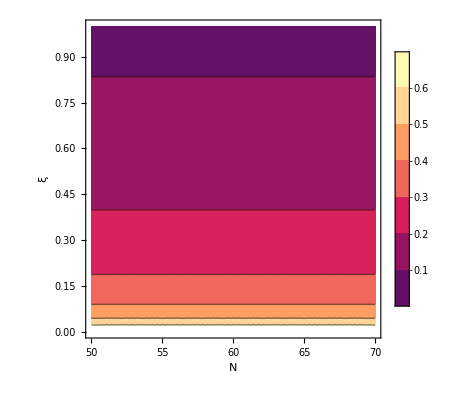

```mathematica
ContourPlot[finalplot[1.810037690193486*10^-10,ξ,eN]/0.01,{eN,50,70},{ξ,0.0001,1},FrameLabel->{"N","ξ"},PlotLegends->Automatic,LabelStyle->Directive[Black,Bold]]
```

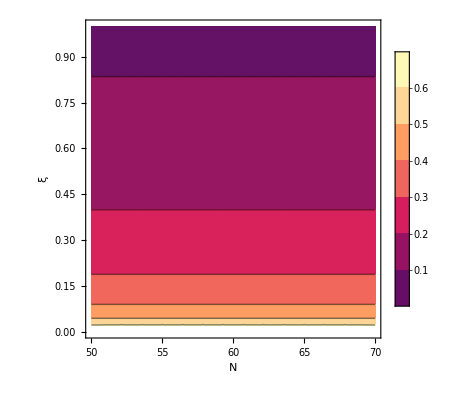

```mathematica
xicon=ContourPlot[finalplotlqg[1.810037690193486*10^-10,ξ,eN]/0.01,{eN,50,70},{ξ,0.0001,1},FrameLabel->{"N","ξ"},PlotLegends->Automatic,LabelStyle->Directive[Black,Bold]]
```

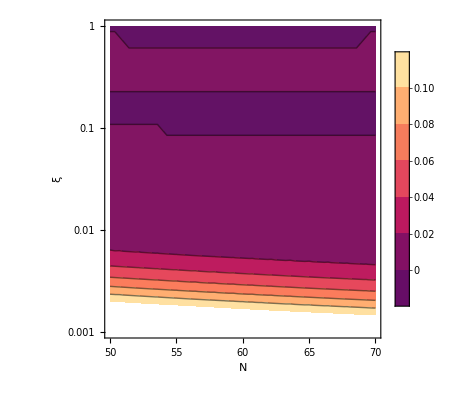

```mathematica
xicondif=ContourPlot[(finalplotlqg[1.810037690193486*10^-10,ξ,eN]-finalplot[1.810037690193486*10^-10,ξ,eN])/0.01,{eN,50,70},{ξ,0.001,1},FrameLabel->{"N","ξ"},PlotLegends->Automatic,ScalingFunctions->{"Linear","Log","Linear"},LabelStyle->Directive[Black,Bold]]
```

```mathematica
Plot3D[finalplot[λ,0.001,eN]/800,{eN,50,70},{λ,0,1},AxesLabel->{"N","λ","𝒫"},LabelStyle->Directive[Black,Bold]]
```

-Graphics3D-

```mathematica
lam=Plot3D[finalplotlqg[λ,0.001,eN]/800,{eN,50,70},{λ,0,1},AxesLabel->{"N","λ","𝒫"},LabelStyle->Directive[Black,Bold]]
```

-Graphics3D-

```mathematica
lamdif=Plot3D[(finalplotlqg[λ,0.001,eN]-finalplot[λ,0.001,eN])/800,{eN,50,70},{λ,0,1},AxesLabel->{"N","λ","𝒫_LQG-𝒫_GR"},LabelStyle->Directive[Black,Bold]]
```

-Graphics3D-

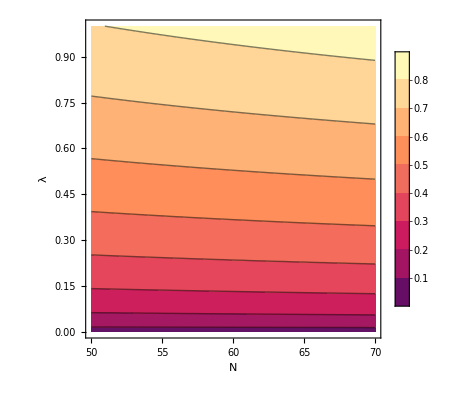

```mathematica
ContourPlot[finalplot[λ,0.001,eN]/800,{eN,50,70},{λ,0,1},FrameLabel->{"N","λ"},PlotLegends->Automatic,LabelStyle->Directive[Black,Bold]]
```

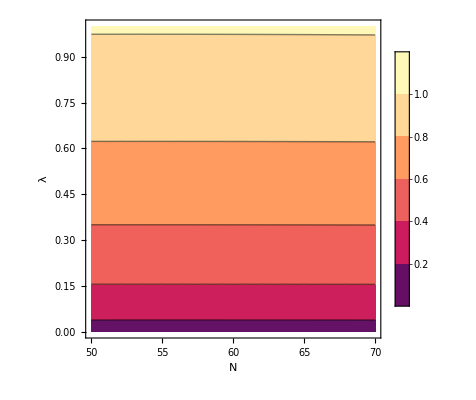

```mathematica
lamcon=ContourPlot[finalplotlqg[λ,0.001,eN]/800,{eN,50,70},{λ,0,1},FrameLabel->{"N","λ"},PlotLegends->Automatic,LabelStyle->Directive[Black,Bold]]
```

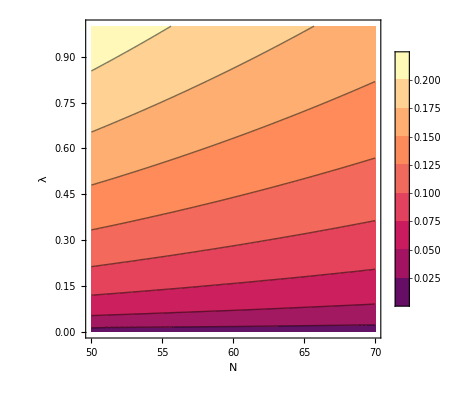

```mathematica
lamcondif=ContourPlot[(finalplotlqg[λ,0.001,eN]-finalplot[λ,0.001,eN])/800,{eN,50,70},{λ,0,1},FrameLabel->{"N","λ"},PlotLegends->Automatic,LabelStyle->Directive[Black,Bold]]
```

```mathematica
SetDirectory[NotebookDirectory[]];Export["1_3_3d_xi.pdf",xi,ImageResolution->300];Export["1_3_3d_xi_diff.pdf",xidif,ImageResolution->300];Export["1_3_con_xi.pdf",Rasterize[xicon,"Image",ImageResolution->300],ImageResolution->300];
Export["1_3_con_xi_diff.pdf",Rasterize[xicondif,"Image",ImageResolution->300],ImageResolution->300];
```